```mathematica
Integrate[Exp[-2I*k*x]+Exp[2I*k*x],{x,-Infinity,0}]
```

ConditionalExpression[ComplexInfinity, Im[k]<0]

```mathematica
Integrate[Exp[-2I*k*x]+Exp[2I*k*x],x]
```

(ⅈ ⅇ^(-2 ⅈ k x))/(2 k)-(ⅈ ⅇ^(2 ⅈ k x))/(2 k)

```mathematica
Integrate[Sin[k*x]^2,x]
```

x/2-Sin[2 k x]/(4 k)

```mathematica
Integrate[(Subscript[A, 1] Cos[k*x]+Subscript[A, 2] Sin[k*x])^2,x]
```

((2 k x+Sin[2 k x]) A_1^2-2 Cos[2 k x] A_1 A_2-(-2 k x+Sin[2 k x]) A_2^2)/(4 k)

```mathematica
Solve[√(e/(Subscript[V, 0]-e))==-Tan[√((2m*e)/ℏ^2)a],e]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[√(e/(-e+V_0))==-Tan[√2 a √((e m)/ℏ^2)],e]

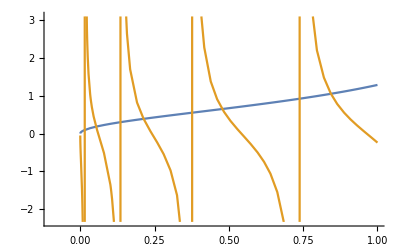

```mathematica
Plot[{√(e/(1.602176565*10^-18-e)),-Tan[√((2*9.10938291*10^-31*e)/((1.054571726*10^-34)^2))*10^-9]},{e,-10^-19,10^-18}]
```